### 5. Starobinsky Potential Part Two: Changing initial value to phi(0.001) = -200

### ***Starobinsky Approximation: I’m going to use the approximation V ~ (1-e^-ϕ)^2 just to make it easier,

### Below is the equation for the Starobinsky potential (found on Wiki and similarly on Valentino’s Starobinsky Inflationary Potential paper) which is in an inflationary model of the form R + R/(6M^2) found in Table 5 of the Planck 2018 Results paper,

### → V(ϕ) = Λ^4( 1-e^(-√(2/3)ϕ/M_P))^2

### Using the approximation for V given in the Planck paper of V ∝ ϕ^p , we can simplify the equation easier and hopefully get an actual plot for the functions,

→ V(ϕ) = ( 1-e^-ϕ)^2

### Using the same result eqn for ϕ[t] as we got from simplifying Wiltshire’s eqn 3.56 in Section 4: Starobinsky Potential,

ϕ^(..) +3(ȧ)/a ϕ̇+e^-ϕ-e^(-2ϕ)=0

#### And the same result eqn for a[t],

-(ȧ)^2+a^2(ϕ̇)^2+a^2[(1-e^-ϕ)^2]=0

```mathematica
star2=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]+Exp[-ϕ[t]]-Exp[-2*ϕ[t]]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2*((1-Exp[-ϕ[t]])^2)==0,a[0.01]==0.114471,ϕ[0.01]==-200,ϕ'[0.01]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.01, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
Print[a[t]]
```

a[t]

```mathematica
Plot[Evaluate[{a[t],ϕ[t]+1}/.star2],{t,-30,30},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Orange,Purple,Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}]
```

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-29.9988} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-29.9988} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

-Graphics-

This graph is insane, the y-axis is incredibly large I’m not sure it’s correct. Also it’s plotting a green line which is confusing since I only have two functions: one is orange and the other is purple - I’m not even seeing the purple function phi[t]. There may be an (accidental) imaginary number coming up somewhere that’s causing the third plot to show up?? 

I’m going to try to zoom in on the green line to see what’s happening there.

```mathematica
Plot[Evaluate[{a[t],ϕ[t]+1}/.star2],{t,-10,10},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotRange->{0,10^(87)},PlotStyle->{Orange,Purple,Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}]
```

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-9.99959} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-9.99959} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

-Graphics-

```mathematica
Manipulate[Plot[Evaluate[{a[t],ϕ[t]+1}/.star2],{t,-30,30},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotRange->{0,Max},PlotStyle->{Orange,Purple,Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}],{{Max,0},10^(87),10^(176),VerticalSlider,Appearance->"Labeled"},ControlPlacement->{Left}]
```

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-29.9988} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-29.9988} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-29.9988} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-29.9988} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

ReplaceAll::reps: {star2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::prng: Value of option PlotRange -> {0,Max$$} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ReplaceAll::reps: {star2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {star2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::prng: Value of option PlotRange -> {0,Max$$} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ReplaceAll::reps: {star2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

### ***Starobinsky Re-do: I’m going to use the approximation V ~ (1-e^(+ϕ))^2 just to flip the potential over the x-axis,

ϕ^(..) +3(ȧ)/a ϕ̇+1/2 d/dϕ[(1-e^ϕ)^2]=0
ϕ^(..) +3(ȧ)/a ϕ̇-e^ϕ+e^(2ϕ)=0

### Now for a[t] (eqn 3.56),

-(ȧ)^2+a^2(ϕ̇)^2+a^2[(1-e^ϕ)^2]=0 
-(ȧ)^2+a^2(ϕ̇)^2+a^2(1-2 e^ϕ+e^(2ϕ))=0

```mathematica
star4=NDSolve[{ϕ''[t]+(3a'[t]ϕ'[t])/a[t]-Exp[ϕ[t]]+Exp[2*ϕ[t]]==0, -(a'[t])^2+(a[t])^2(ϕ'[t])^2+(a[t])^2*((1-Exp[-ϕ[t]])^2)==0,a[0.005]==0.114471,ϕ[0.005]==-200,ϕ'[0.005]==333.333},{a,ϕ},{t,0.005,2}]
```

NDSolve::ndsz: At t == 0.005, step size is effectively zero; singularity or stiff system suspected.

{{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]},{a→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[{a[t],ϕ[t]+1}/.star4],{t,-30,30},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Blue,Orange,Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}]
```

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

This graph looks better than the  -phi graph above, although there’s still a large y-axis scale and there’s also the extra green line again which I’m not sure what that is. But in this graph, a[t] is basically a reflection over the x-axis of phi[t] .

```mathematica
Plot[Evaluate[{a[t],ϕ[t]+1}/.star4],{t,-30,30},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotRange->{-10^(90),10^(90)},PlotStyle->{Blue,Orange,Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}]
```

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Manipulate[Plot[Evaluate[{a[t],ϕ[t]+1}/.star4],{t,-30,30},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotRange->{-10^(90),Max1},PlotStyle->{Blue,Orange,Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}],{{Max1,0},10^(89),10^(92),VerticalSlider,Appearance->"Labeled"},ControlPlacement->{Left}]
```

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ReplaceAll::reps: {star4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Plot[{a[t]}/.star4,{t,-50,50},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Blue,Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}]
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[{ϕ[t]}/.star4,{t,-50,50},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","f(t)"},PlotStyle->{Orange,Thickness[0.009]},PlotLegends->{"a[t]","ϕ[t]"}]
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

### Finally, I’m going to make a parametric plot for a[t] and ϕ[t], Below is a Log[a(t)] plot which appears to increase at an increasing rate for a(t) = (0,0.8) and then increases at a decreasing rate for a(t) = 0.8,20) and it seems to level off after that, infinitely approaching 4.

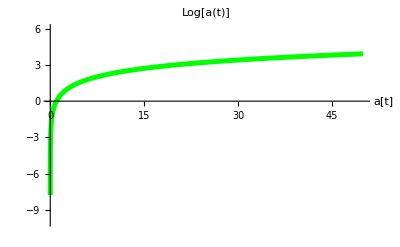

```mathematica
Plot[Log[a[t]],{a[t],-10,50},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"a[t]"},PlotStyle->{Green,Thickness[0.009]},PlotLabel->"Log[a(t)]",PlotRange->{-10,6}]
```

### Finally, I’m going to make a parametric plot for a[t] and ϕ[t],

InterpolatingFunction::dmval: Input value {0.002004} lies outside the range of data in the interpolating function. Extrapolation will be used.

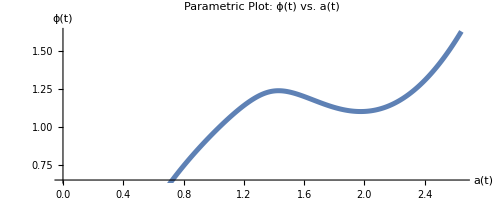

```mathematica
ParametricPlot[Evaluate[{a[t],ϕ[t]+1}/.star4],{t,0.002,4},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"a(t)","ϕ(t)"},PlotPoints->1000,PlotStyle->{Thickness[0.009]},PlotLabel->"Parametric Plot: ϕ(t) vs. a(t)"]
```

### Now, I’m going to just plot the Starobinsky potential and see what it’s like,

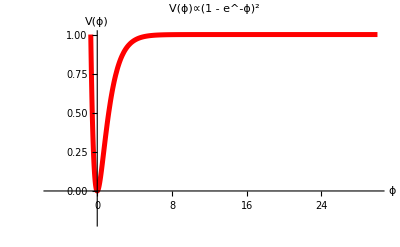

```mathematica
Plot[(1-Exp[-x])^2,{x,-5,30},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"ϕ","V(ϕ)"},PlotStyle->{Red,Thickness[0.009]},PlotLabel->"V(ϕ)∝(1 - e^-ϕ)^2",PlotRange->{-0.2,1}]
```

### We want the potential to be constant for -ϕ , so I’m going to reflect the function over the y-axis by changing the exponent to +ϕ ,

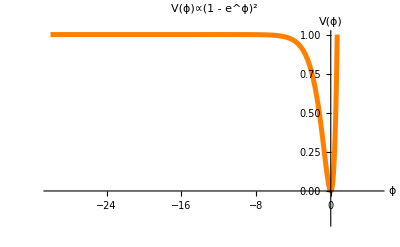

```mathematica
Plot[(1-Exp[x])^2,{x,-30,5},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"ϕ","V(ϕ)"},PlotStyle->{Orange,Thickness[0.009]},PlotLabel->"V(ϕ)∝(1 - e^ϕ)^2",PlotRange->{-0.2,1}]
```

### Now I’m going to make the function less simplistic by including the -sqrt(2/3) term and dividing by the Planck mass in micrograms,

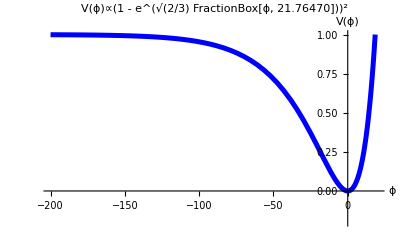

```mathematica
Plot[(1-Exp[(√(2/3))x/(21.76470)])^2,{x,-200,20},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"ϕ","V(ϕ)"},PlotStyle->{Blue,Thickness[0.009]},PlotLabel->"V(ϕ)∝(1 - e^(√(2/3) FractionBox[ϕ, 21.76470]))^2",PlotRange->{-0.2,1}]
```

```mathematica
(* The plot is now more "squished" down vs the previous one which was very stretched up *)
```

```mathematica
Plot3D[{(a)^2(1 - Exp[-ϕ])^2},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "3D Plot a^2 Potential"]
```

-Graphics3D-

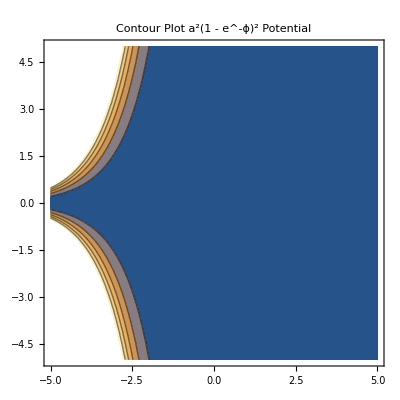

```mathematica
ContourPlot[{(a)^2(1 - Exp[-ϕ])^2},{ϕ, -5, 5},{a,-5,5},  PlotLabel-> "Contour Plot a^2(1 - e^-ϕ)^2 Potential"]
```

```mathematica
Plot3D[{(a)^2(1 - Exp[ϕ])^2},{ϕ, -10, 10},{a,-10,10}, PlotLabel-> "3D Plot a^2 Potential"]
```

-Graphics3D-

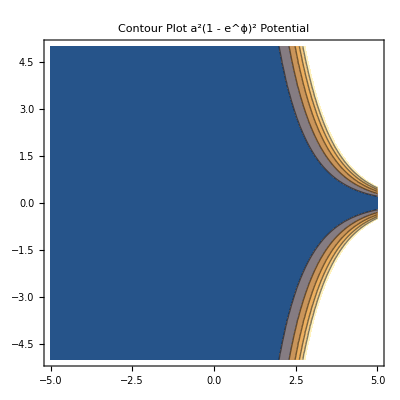

```mathematica
ContourPlot[{(a)^2(1 - Exp[ϕ])^2},{ϕ, -5, 5},{a,-5,5},  PlotLabel-> "Contour Plot a^2(1 - e^ϕ)^2 Potential"]
```